# 旋光物质化学反应反应动力学研究

## ——蔗糖转化反应

## 数据导入与初始化

```mathematica
<<draw.wl
<<file.wl
<<fitting.wl
```

```mathematica
SetDirectory[path]
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry

```mathematica
path="/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry";
rawdata=Import[path<>"/Kecai_Xuan/exp7/data/data.xlsx"];
```

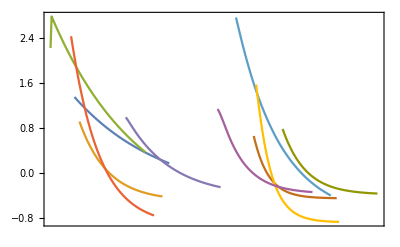

```mathematica
DateListPlot[rawdata]
```

```mathematica
name={{1->"30度-低糖-低酸"},{2->"30度-低糖-高酸"},{3->"30度-高糖-低酸"},{4->"30度-高糖-高酸"},{5->"35度-低糖-低酸"},{6->"35度-低糖-高酸"},{7->"35度-高糖-低酸"},{8->"35度-高糖-高酸"},{9->"40度-低糖-低酸-1"},{10->"40度-低糖-低酸-2"}};
name=name//Flatten;
```

```mathematica
absolute = Table[AbsoluteTime[rawdata[[i, 1, 1]]], {i, 1, 10}];
inf = {-0.4525,-0.4814,-0.9046,-0.9253,-0.2103,-0.4476,-0.8321,-0.8528,-0.3739,-0.3920};
```

```mathematica
data = rawdata;

For[i = 1, i <= 10, i++,
    l = Length[data[[i]]];
    For[j = 1, j <= l, j++,
        data[[i,j,1]] = AbsoluteTime[data[[i,j,1]]];
    ]
]
For[i = 1, i <= 10, i++,
    l = Length[data[[i]]];
    For[j = 1, j <= l, j++,
        data[[i,j,1]] = data[[i,j,1]] - absolute[[i]];
    ]
]
```

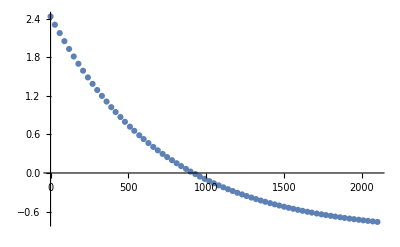

```mathematica
ListPlot[data[[4]]]
```

## 线性拟合

### 对数修正

```mathematica
For[i = 1, i <= 10, i++,
    l = Length[data[[i]]];
    For[j = 1, j <= l, j++,
        data[[i,j,2]] = Log[data[[i,j,2]]-inf[[i]]];
    ]
]
```

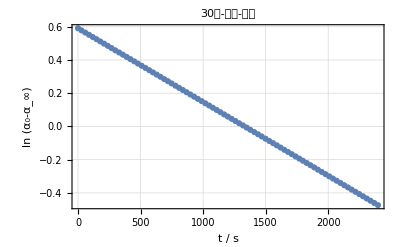
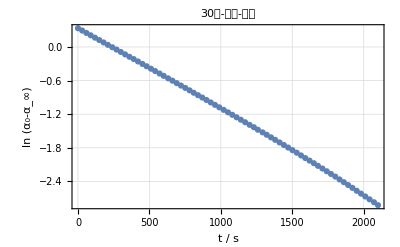
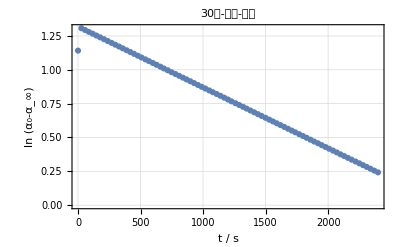
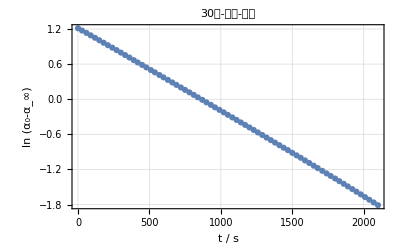
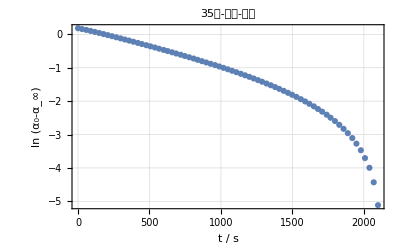
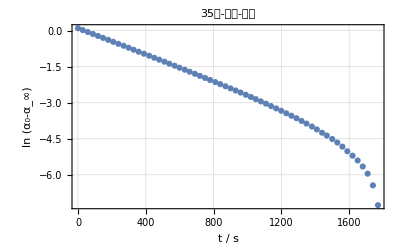
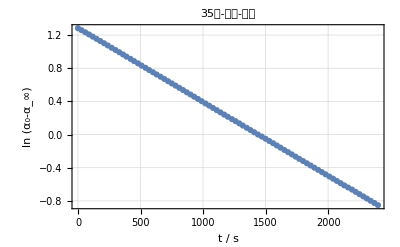
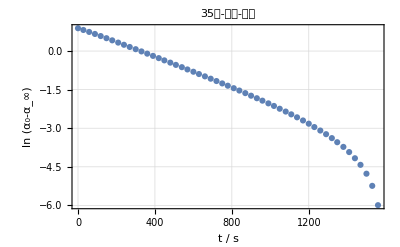

```mathematica
Table[ListPlot[data[[i]],PlotTheme->"Detailed",PlotLabel->i/.name,FrameLabel->{"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"}],{i,1,10}]
```

发现有的地方是虚数，取对数变成了复数

### Subscript[α, ∞] 的测量有很大误差，将明显弯曲的数据点舍弃，再进行线性拟合

```mathematica
newdata=data;
```

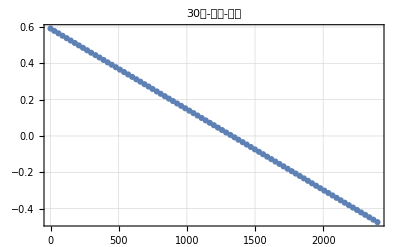
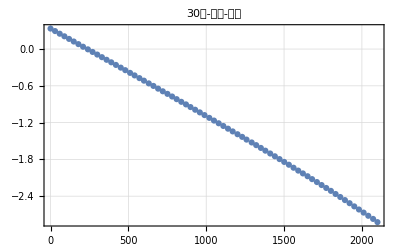
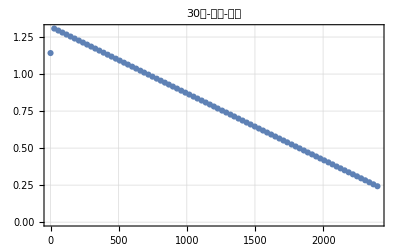
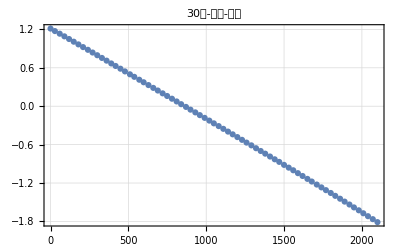
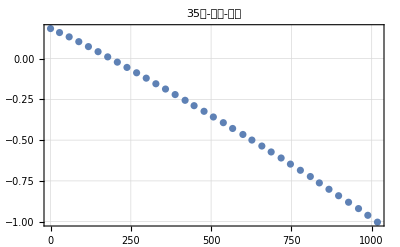
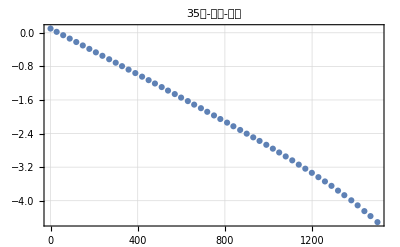
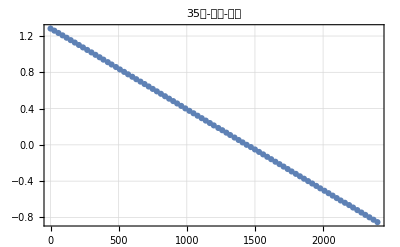
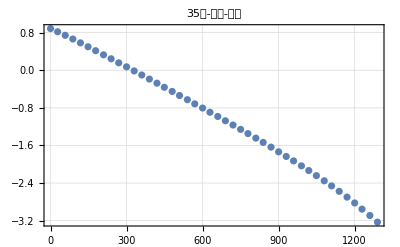

```mathematica
newdata[[5]]=Drop[data[[5]],-46];
newdata[[6]]=Drop[data[[6]],-20];
newdata[[8]]=Drop[data[[8]],-27];
Table[ListPlot[newdata[[i]],PlotTheme->"Detailed",PlotLabel->i/.name],{i,1,10}]
```

```mathematica
linearmodel = Table[LinearModelFit[newdata[[i]], x, x],{i,1,10}];
linearmodel//Column
Table[linearmodel[[i]]["CorrelationMatrix"],{i,1,10}]//Column
```

FittedModel[0.59104-0.000443858 x]
FittedModel[0.371294-0.00148772 x]
FittedModel[1.31047-0.000443837 x]
FittedModel[1.23074-0.00143603 x]
FittedModel[0.220067-0.00116957 x]
FittedModel[0.196733-0.00297584 x]
FittedModel[1.28491-0.0008912 x]
FittedModel[1.00643-0.00311649 x]
FittedModel[0.485241-0.00166394 x]
FittedModel[0.136844-0.00166963 x]

{{1.,-0.863075},{-0.863075,1.}}
{{1.,-0.862856},{-0.862856,1.}}
{{1.,-0.862963},{-0.862963,1.}}
{{1.,-0.862796},{-0.862796,1.}}
{{1.,-0.858938},{-0.858938,1.}}
{{1.,-0.861337},{-0.861337,1.}}
{{1.,-0.863115},{-0.863115,1.}}
{{1.,-0.860642},{-0.860642,1.}}
{{1.,-0.863234},{-0.863234,1.}}
{{1.,-0.863165},{-0.863165,1.}}

#### 计算活化能

```mathematica
k=-Table[linearmodel[[i]]["BestFitParameters"][[2]],{i,1,10}]
t={30,30,30,30,35,35,35,35,40,40}
```

{0.000443858,0.00148772,0.000443837,0.00143603,0.00116957,0.00297584,0.0008912,0.00311649,0.00166394,0.00166963}

{30,30,30,30,35,35,35,35,40,40}

```mathematica
activate[k_,t_,a_,b_]:=Module[
{Ea},
Ea/.Solve[Log[k[[a]]/k[[b]]]==-Ea/R(1/(t[[a]]+273.15)-1/(t[[b]]+273.15)),Ea]
]
```

```mathematica
e=Table[activate[k,t,i,i+4],{i,1,4}]/1000
```

{{150.498},{107.688},{108.284},{120.355}}

```mathematica
Table[(e[[i]]-103.55)/103.55,{i,4}]
```

{{0.453388},{0.0399643},{0.0457128},{0.162289}}

#### 结论：线性相关系数较低，废弃不用，需要换为非线性拟合

### 按照线性拟合的要求继续做

#### 准备绘图

```mathematica
ModelLegends[linearmodel,t]
```

{{0.59104 + -0.000443858 t},{0.371294 + -0.00148772 t},{1.31047 + -0.000443837 t},{1.23074 + -0.00143603 t},{0.220067 + -0.00116957 t},{0.196733 + -0.00297584 t},{1.28491 + -0.0008912 t},{1.00643 + -0.00311649 t},{0.485241 + -0.00166394 t},{0.136844 + -0.00166963 t}}

```mathematica
linearmodellegends={{"0.59104 - 0.000443858 t"},{"0.371294 - 0.00148772 t"},{"1.31047 - 0.000443837 t"},{"1.23074 - 0.00143603 t"},{"0.220067 - 0.00116957 t"},{"0.196733 - 0.00297584 t"},{"1.28491 - 0.0008912 t"},{"1.00643 - 0.00311649 t"},{"0.485241 - 0.00166394 t"},{"0.136844 - 0.00166963 t"}}
```

{{0.59104 - 0.000443858 t},{0.371294 - 0.00148772 t},{1.31047 - 0.000443837 t},{1.23074 - 0.00143603 t},{0.220067 - 0.00116957 t},{0.196733 - 0.00297584 t},{1.28491 - 0.0008912 t},{1.00643 - 0.00311649 t},{0.485241 - 0.00166394 t},{0.136844 - 0.00166963 t}}

```mathematica
todraw=Table[linearmodel[[i]][t],{i,1,10}]
```

{0.59104-0.000443858 t,0.371294-0.00148772 t,1.31047-0.000443837 t,1.23074-0.00143603 t,0.220067-0.00116957 t,0.196733-0.00297584 t,1.28491-0.0008912 t,1.00643-0.00311649 t,0.485241-0.00166394 t,0.136844-0.00166963 t}

#### 分别绘制

```mathematica
plotRespectively=ListPlot[#1,Frame -> True, LabelStyle
     -> Directive[Black], GridLines -> Automatic, PlotLegends -> Placed[LineLegend[
    #2, LegendFunction -> Frame], #3],FrameLabel->#4, PlotStyle -> ColorData[
    #5, "ColorList"],PlotRange->#6]&;
```

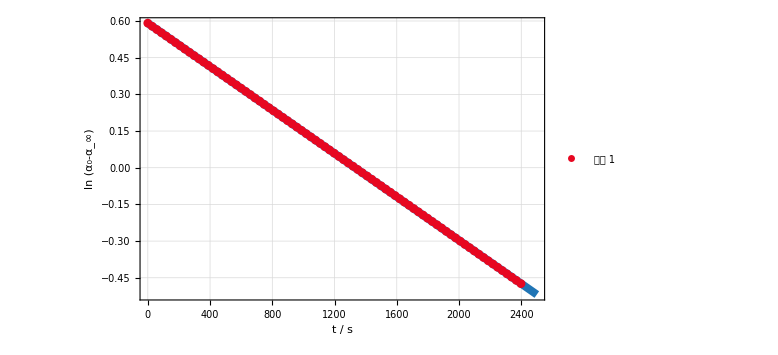

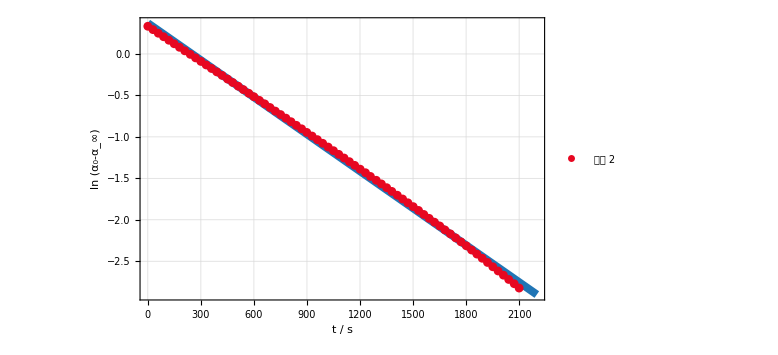

```mathematica
point1=plotRespectively[data[[1]],{"组别 1"},{0.8,0.8},{"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"},3,Full];
point2=plotRespectively[data[[2]],{"组别 2"},{0.8,0.8},{"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"},3,Full];

line1= Plot[todraw[[1]], {t, 0, 2500}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend["xzcv", LegendFunction -> Frame
    ], {0.8,0.8}], FrameLabel -> {"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"}, PlotStyle -> Directive[Thickness[0.01],ColorData[99,"ColorList"]], ImageSize -> Large];
line2= Plot[todraw[[2]], {t, 0, 2200}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend["xzcv", LegendFunction -> Frame
    ], {0.8,0.8}], FrameLabel -> {"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"}, PlotStyle -> Directive[Thickness[0.01],ColorData[99,"ColorList"]], ImageSize -> Large];
    
first=Show[line1,point1]
second=Show[line2,point2]
```

```mathematica
Export["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp7/first.jpg",first]
Export["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp7/second.jpg",second]
```

#### 绘制于一张图中

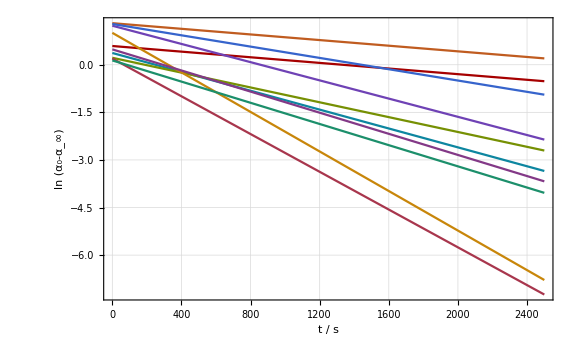

```mathematica
lines=Plot[todraw, {t, 0, 2500}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend["xzcv", LegendFunction -> Frame
    ], {0.8,0.8}], FrameLabel -> {"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"}, PlotStyle -> ColorData[99,"ColorList"], ImageSize -> Large]
```

```mathematica
legends=Table["组别 "<>ToString[i],{i,1,10}];
place=Table[{0.1,0.2},{i,1,10}];
framelabel=Table[{"t / s","ln (\!\(\*SubscriptBox[\(α\), \(0\)]\)-\!\(\*SubscriptBox[\(α\), \(∞\)]\))"},{i,1,10}];
place=Table[{0.1,0.35},{i,1,10}];

InOne = ListPlot[#1,Frame -> True, LabelStyle -> Directive[Black], GridLines -> Automatic,
    FrameLabel->#4, PlotStyle -> ColorData[#5, "ColorList"],PlotRange->#6,ImageSize->Large]&;
    InOneLine = Plot[#1,{t, 0, 2500},Frame -> True, LabelStyle -> Directive[Black], GridLines -> Automatic, 
    PlotLegends -> Placed[LineLegend[ColorData[#5, "ColorList"], #2//Flatten, LegendFunction -> Frame], #3],
    FrameLabel->#4, PlotStyle -> ColorData[#5, "ColorList"],PlotRange->#6,ImageSize->Large]&;
```

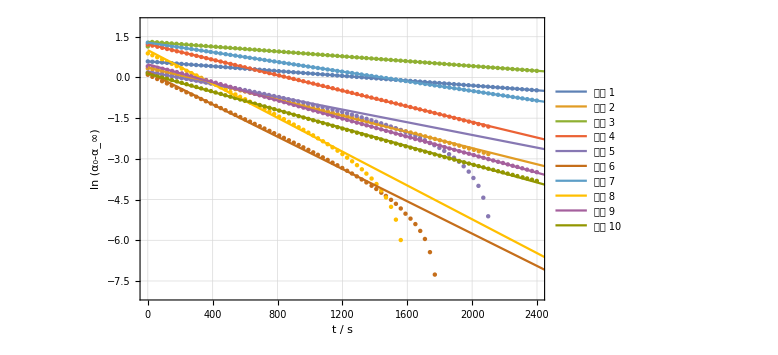

```mathematica
points=InOne[data,legends,place[[1]],framelabel[[1]],97,{-8,2}];

lines=InOneLine[todraw,legends,place[[1]],framelabel[[1]],97,{-8,2}];

Show[points,lines]
inone=%;
```

```mathematica
Export["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp7/inone.jpg",inone]
```

#### 计算初始旋光度

```mathematica
initial=Table[linearmodel[[i]]["BestFitParameters"][[1]],{i,1,10}];
```

```mathematica
Table[Solve[Log[x-inf[[i]]]==initial[[i]],x],{i,1,10}]//Flatten
```

#### 残差分析

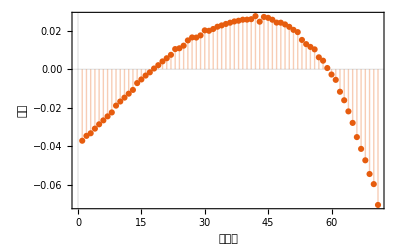

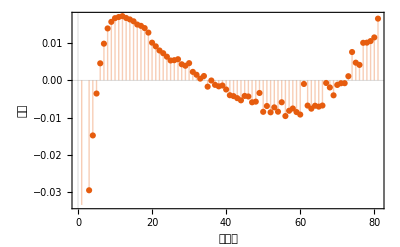

```mathematica
residual=Table[ListPlot[linearmodel[[i]]["FitResiduals"],Filling->Axis,PlotTheme->"Scientific",FrameLabel->{"数据点","残差"}],{i,1,10}];
residual2=ListPlot[linearmodel[[2]]["FitResiduals"],Filling->Axis,PlotTheme->"Scientific",FrameLabel->{"数据点","残差"}]
residual9=ListPlot[linearmodel[[9]]["FitResiduals"],Filling->Axis,PlotTheme->"Scientific",FrameLabel->{"数据点","残差"}]
```

```mathematica
linearmodel[[9]]["StudentizedResiduals"]
```

{-6.88115,-4.06091,-2.33047,-1.13809,-0.271117,0.34702,0.750436,1.0657,1.2028,1.2794,1.30265,1.31993,1.28029,1.24889,1.20923,1.14093,1.11302,1.06575,0.972388,0.764838,0.689214,0.604792,0.548763,0.477881,0.400479,0.406718,0.425875,0.323688,0.293828,0.346058,0.169762,0.111902,0.0335945,0.0864255,-0.128287,-0.00422109,-0.0922273,-0.122087,-0.104895,-0.18553,-0.300991,-0.31907,-0.360179,-0.404067,-0.315263,-0.326355,-0.443987,-0.4308,-0.255827,-0.637523,-0.519721,-0.647981,-0.547651,-0.635507,-0.444441,-0.724622,-0.61706,-0.571052,-0.644433,-0.695506,-0.0743307,-0.512831,-0.575949,-0.516498,-0.535017,-0.512817,-0.0543608,-0.145389,-0.305796,-0.0944989,-0.0602138,-0.0593549,0.0831563,0.577933,0.360202,0.314838,0.769518,0.773772,0.80677,0.883433,1.27895}

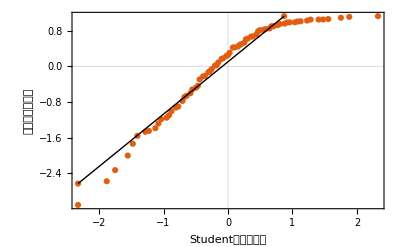

```mathematica
qq=QuantilePlot[linearmodel[[2]]["StudentizedResiduals"],Table[InverseCDF[NormalDistribution[],q],{q,1/100,99/100,1/100}],PlotTheme->"Scientific",FrameLabel->{"Student分布分位数","实际数据分位数"}]
```

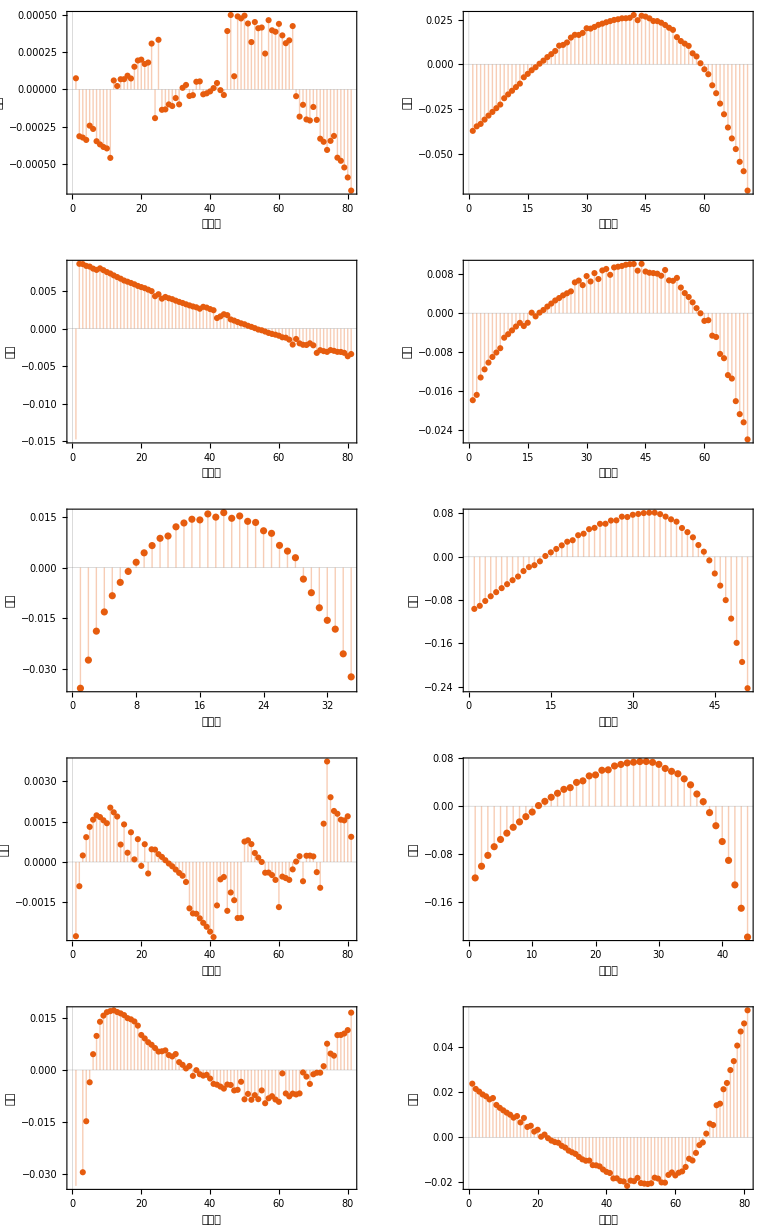

```mathematica
residualassemble=GraphicsGrid[Partition[residual,2]]
```

```mathematica
Export["/Users/royalty/Desktop/residual2.jpg",residual2]
Export["/Users/royalty/Desktop/residual9.jpg",residual9]
```

/Users/royalty/Desktop/residual2.jpg

/Users/royalty/Desktop/residual9.jpg

```mathematica
Export["/Users/royalty/Desktop/qq.jpg",qq]
```

/Users/royalty/Desktop/qq.jpg

从残差图中很明显可以看出，有某种很明显的模式在使数据点偏离一级反应

### 下面进行非线性拟合

## 非线性拟合

### 重新导入

```mathematica
path="/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry";
rawdata=Import[path<>"/Kecai_Xuan/exp7/data/data.xlsx"];
name={{1->"30度-低糖-低酸"},{2->"30度-低糖-高酸"},{3->"30度-高糖-低酸"},{4->"30度-高糖-高酸"},{5->"35度-低糖-低酸"},{6->"35度-低糖-高酸"},{7->"35度-高糖-低酸"},{8->"35度-高糖-高酸"},{9->"40度-低糖-低酸-1"},{10->"40度-低糖-低酸-2"}};
name=name//Flatten;
absolute = Table[AbsoluteTime[rawdata[[i, 1, 1]]], {i, 1, 10}];
inf = {-0.4525,-0.4814,-0.9046,-0.9253,-0.2103,-0.4476,-0.8321,-0.8528,-0.3739,-0.3920};

data=rawdata;
For[i = 1, i <= 10, i++,
    l = Length[data[[i]]];
    For[j = 1, j <= l, j++,
        data[[i,j,1]] = AbsoluteTime[data[[i,j,1]]];
    ]
]
For[i = 1, i <= 10, i++,
    l = Length[data[[i]]];
    For[j = 1, j <= l, j++,
        data[[i,j,1]] = data[[i,j,1]] - absolute[[i]];
    ]
]
(*得到以秒为单位的绝对时间*)
```

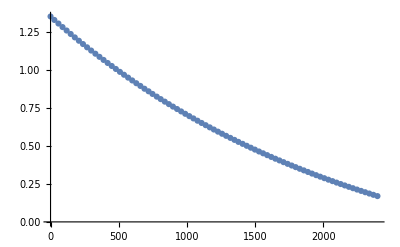

```mathematica
ListPlot[data[[1]]]
```

### 自定义函数的回归分析

#### 建立回归模型

```mathematica
Clear["Global`*"]
```

{t}↦1.80937 ⅇ^(-0.000442077 t)-0.456628

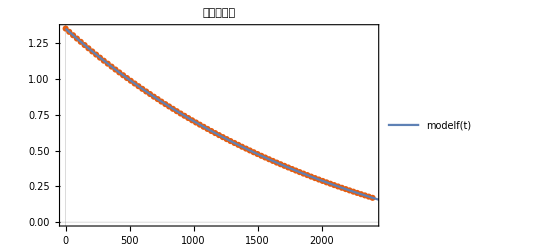

```mathematica
nonlineardata = data;

Clear[{Subscript[α, 0],Subscript[α, ∞],k}]
model=(Subscript[α, 0]-Subscript[α, ∞])E^(-k t)+Subscript[α, ∞];

nonlinearfit=FindFit[nonlineardata[[1]],model,{Subscript[α, 0],Subscript[α, ∞],k},t];
modelf=Function[{t},Evaluate[model/.nonlinearfit]];
TraditionalForm[modelf]

Show[ListPlot[nonlineardata[[1]],PlotLabel->HoldForm[非线性回归],PlotTheme->"Scientific"],Plot[modelf[t],{t,0,2500},PlotTheme->"Detailed"]]
```

```mathematica
model=(a0-a1)E^(-k t)+a1;

nonlinearfit = Table[FindFit[nonlineardata[[i]],model,{a0,a1,k},t],{i,1,10}];
nonlinearmodel = Table[Function[{t},Evaluate[model/.(nonlinearfit[[i]])]],{i,1,10}];
nonlinearmodel//Column
nonlinearfit//Column
```

Function[{t},-0.456628+1.80937 ⅇ^(-0.000442077 t)]
Function[{t},-0.498607+1.4129 ⅇ^(-0.00138846 t)]
Function[{t},-1.32222+4.08155 ⅇ^(-0.000372025 t)]
Function[{t},-0.944475+3.3913 ⅇ^(-0.00139361 t)]
Function[{t},-0.434931+1.43886 ⅇ^(-0.000873256 t)]
Function[{t},-0.456416+1.11372 ⅇ^(-0.00268671 t)]
Function[{t},-0.830533+3.61579 ⅇ^(-0.000892884 t)]
Function[{t},-0.887667+2.49847 ⅇ^(-0.00272272 t)]
Function[{t},-0.388873+1.59848 ⅇ^(-0.00157185 t)]
Function[{t},-0.389595+1.17091 ⅇ^(-0.0017125 t)]

{a0→1.35274,a1→-0.456628,k→0.000442077}
{a0→0.914294,a1→-0.498607,k→0.00138846}
{a0→2.75933,a1→-1.32222,k→0.000372025}
{a0→2.44682,a1→-0.944475,k→0.00139361}
{a0→1.00393,a1→-0.434931,k→0.000873256}
{a0→0.657306,a1→-0.456416,k→0.00268671}
{a0→2.78526,a1→-0.830533,k→0.000892884}
{a0→1.6108,a1→-0.887667,k→0.00272272}
{a0→1.20961,a1→-0.388873,k→0.00157185}
{a0→0.781318,a1→-0.389595,k→0.0017125}

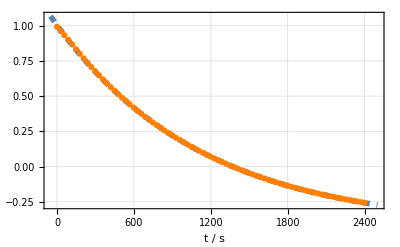

```mathematica
Show[Plot[nonlinearmodel[[5]][t], {t, -50, 2500}, PlotTheme -> "Detailed",PlotLegends->None,
      Frame -> True, FrameLabel -> {"t / s", ""
    }, PlotStyle -> Directive[Dashed, Thickness[0.01]]], ListPlot[nonlineardata
    [[5]],  PlotStyle -> Orange]]
```

```mathematica
Export["/Users/royalty/Desktop/nonlinear.jpg",%]
```

/Users/royalty/Desktop/nonlinear.jpg

```mathematica
l0=Table[nonlinearmodel[[5]][t],{t,time}]
```

{1.00393,0.969174,0.932867,0.897499,0.863046,0.829484,0.796789,0.76494,0.733914,0.703691,0.674249,0.645568,0.617629,0.590413,0.563028,0.538923,0.512913,0.489211,0.464529,0.442037,0.41787,0.397271,0.375044,0.35479,0.333698,0.314477,0.294462,0.274982,0.257834,0.239921,0.222471,0.204913,0.187824,0.172251,0.156551,0.141257,0.126358,0.111845,0.0972415,0.0834808,0.070076,0.0570178,0.0442972,0.0323134,0.0198344,0.00807527,-0.00337976,-0.0141713,-0.0254089,-0.0359981,-0.045974,-0.0560314,-0.066151,-0.0756867,-0.0849759,-0.0943224,-0.10284,-0.111144,-0.120067,-0.127404,-0.135617,-0.143357,-0.150896,-0.158241,-0.16563,-0.172365,-0.179377,-0.185768,-0.192422,-0.198693,-0.204802,-0.210752,-0.216549,-0.222196,-0.227696,-0.233055,-0.238275,-0.24336,-0.248314,-0.253139,-0.25753}

```mathematica
数据点 残差
```

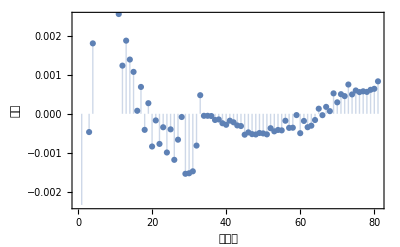

```mathematica
l0=Table[nonlinearmodel[[5]][t],{t,time}];
Length[nonlineardata[[5]]];
residualnonlinear5=Table[nonlineardata[[5,i,2]]-l0[[i]],{i,81}];
ListPlot[residualnonlinear5,Frame->True,FrameLabel -> {"数据点", "残差"
    },Filling->Axis]
```

```mathematica
Export["/Users/royalty/Desktop/renonlinear.jpg",%]
```

/Users/royalty/Desktop/renonlinear.jpg

```mathematica
modelplot = Plot[#2[t], {t, #1[[1, 1]], #1[[Length[#1], 1]]}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend[#3, LegendFunction -> Frame
    ], #4], FrameLabel -> #5, PlotStyle -> #6, ImageSize -> Large]&;
```

#### 符号回归

```mathematica
symregression=Table[FindFormula[data[[i]]],{i,1,10}](*MATHEMATICA内置函数，直接找到一组数据的最佳拟合，可能会与其他方法得到的结果有出入*)
```

```mathematica
Show[Plot[f[t], {t, 0, 2397}, PlotTheme -> "Detailed",
     PlotLegends -> {"f(t)"
    }, Frame -> True, PlotStyle -> Directive[Dashed, Thickness[0.01]]], ListPlot[nonlineardata
    [[5]], PlotLegends -> {"组别 5"}, PlotStyle -> Orange]]
```

## 对副反应的探究

```mathematica
residualassemble
```

### 如果同时伴有一个未知的二级副反应

```mathematica
sol=NDSolve[{c'[t]==-14.88*10^-4 c[t]- c[t]^2,c[0]==0.33411231132958863},c,t][[1]]
```

```mathematica
Manipulate[sol=NDSolve[{c'[t]==-14.88*10^-4 c[t]-n c[t]^2,c[0]==0.9153},c,t][[1]];
    Plot[Evaluate[c[t]/.sol],{t,20,1000}],{n,1,10}]
```

```mathematica
Plot[Evaluate[c[t]/.sol],{t,20,1000}]
```

```mathematica
DSolve[c'[t]==-k1 c[t],c,t]
```

```mathematica
data[[2]]
```

```mathematica
DSolve[{c'[t]==-k1 c[t]-k2 c[t]^2},c,t][[1,1,2,2]]/.C[1]->c1
```

```mathematica
model = -(Sqrt[k1]/Sqrt[E^(2 k1 (-c1+t))-k2])

nonlinearfit = Table[FindFit[nonlineardata[[i]],model,{k1,k2,c1},t],{i,1,10}];
nonlinearmodel = Table[Function[{t},Evaluate[model/.(nonlinearfit[[i]])]],{i,1,10}];
nonlinearmodel//Column
nonlinearfit//Column
```

```mathematica
nonlineardata
```

```mathematica
DSolve[{c'[t]==-k1 c[t]^2,c[0]==c0},c,t][[1,1,2,2]]
```

```mathematica
g[t_]:=1/(1+1 *0.1 t)
```

```mathematica
Plot[Log[g[t]],{t,0,100}]
```

```mathematica
ListPlot[Table[Log[g[t]],{t,0,100}]]
```

```mathematica
Clear[c,t]
```

#### 结论：假设不成立

### 猜测：生成物以一级分解

```mathematica
DSolve[{c1'[t]==-k1 c1[t],c2'[t]==k1 c1[t]-k2 c2[t],c1[0]==c0,c2[0]==0},{c1,c2},t]
```

```mathematica
rotate[t_] := a1 c0 E^(-k1 t) - a2 (c0 E^(-k1 t-k2 t) (-E^(k1 t)+E^(k2 t)) k1)/(k1-k2)
```

```mathematica
-((c0 E^(-k1 t-k2 t) (-E^(k1 t)+E^(k2 t)) k1)/(k1-k2))//TeXForm
```

```mathematica
rotate[0]
Limit[rotate[t],t->∞]
rotate[t]
```

```mathematica
Solve[rotate'[t]==0,t]
Solve[rotate''[t]==0,t]
```

```mathematica
rotate[t]
```

```mathematica
Log[(-a1 k1+a2 k1+a1 k2)/(a2 k2)]/(k1-k2)//TeXForm
```

```mathematica
Log[(-a1 k1+a2 k1+a1 k2)/(a2 k2)]/(k1-k2)//TeXForm
```

## 数据表格输出

```mathematica
rawdata[[1,1]]
DateString/@rawdata[[1,1]]
```

{Fri 30 Sep 2022 16:29:33GMT+8,1.3535}

{Fri 30 Sep 2022 16:29:33,Mon 1 Jan 1900 00:00:01}

```mathematica
output=rawdata
```

{{{Fri 30 Sep 2022 16:29:33GMT+8,1.3535},{Fri 30 Sep 2022 16:30:01GMT+8,1.3305},{Fri 30 Sep 2022 16:30:31GMT+8,1.3069},{Fri 30 Sep 2022 16:31:01GMT+8,1.2836},74,{Fri 30 Sep 2022 17:08:31GMT+8,0.1869},{Fri 30 Sep 2022 17:09:01GMT+8,0.1784},{Fri 30 Sep 2022 17:09:31GMT+8,0.17}},8,{1}}
 |  |  |  |

```mathematica
out4=rawdata[[4]];
out8=rawdata[[8]];
```

```mathematica
For[i=1,i<=Length[out8],i++,
    out8[[i,1]]=DateString[rawdata[[8,i,1]]]
]
a=Take[out8,36];
b=Take[out8,-35];
Join[a,b,2]
Export["/Users/royalty/Desktop/dump.txt",%]
```

{{Fri 30 Sep 2022 17:46:08,1.5755,Fri 30 Sep 2022 18:04:08,-0.7576},{Fri 30 Sep 2022 17:46:36,1.4162,Fri 30 Sep 2022 18:04:37,-0.7674},{Fri 30 Sep 2022 17:47:06,1.2514,Fri 30 Sep 2022 18:05:07,-0.7767},{Fri 30 Sep 2022 17:47:36,1.0914,Fri 30 Sep 2022 18:05:38,-0.7855},{Fri 30 Sep 2022 17:48:06,0.9393,Fri 30 Sep 2022 18:06:08,-0.7934},{Fri 30 Sep 2022 17:48:36,0.7966,Fri 30 Sep 2022 18:06:37,-0.8007},{Fri 30 Sep 2022 17:49:06,0.6641,Fri 30 Sep 2022 18:07:08,-0.8073},{Fri 30 Sep 2022 17:49:37,0.5368,Fri 30 Sep 2022 18:07:38,-0.8133},{Fri 30 Sep 2022 17:50:07,0.4238,Fri 30 Sep 2022 18:08:08,-0.8189},{Fri 30 Sep 2022 17:50:37,0.3189,Fri 30 Sep 2022 18:08:36,-0.8239},{Fri 30 Sep 2022 17:51:08,0.2225,Fri 30 Sep 2022 18:09:08,-0.8287},{Fri 30 Sep 2022 17:51:38,0.1334,Fri 30 Sep 2022 18:09:38,-0.8331},{Fri 30 Sep 2022 17:52:08,0.0515,Fri 30 Sep 2022 18:10:08,-0.8373},{Fri 30 Sep 2022 17:52:38,-0.0237,Fri 30 Sep 2022 18:10:37,-0.8408},{Fri 30 Sep 2022 17:53:08,-0.0928,Fri 30 Sep 2022 18:11:08,-0.8443},{Fri 30 Sep 2022 17:53:37,-0.1565,Fri 30 Sep 2022 18:11:38,-0.8475},{Fri 30 Sep 2022 17:54:08,-0.2151,Fri 30 Sep 2022 18:12:08,-0.8503},{Fri 30 Sep 2022 17:54:37,-0.2687,Fri 30 Sep 2022 18:12:38,-0.8531},{Fri 30 Sep 2022 17:55:08,-0.3181,Fri 30 Sep 2022 18:13:08,-0.8554},{Fri 30 Sep 2022 17:55:37,-0.3635,Fri 30 Sep 2022 18:13:38,-0.8577},{Fri 30 Sep 2022 17:56:08,-0.4051,Fri 30 Sep 2022 18:14:08,-0.8598},{Fri 30 Sep 2022 17:56:37,-0.4435,Fri 30 Sep 2022 18:14:38,-0.8616},{Fri 30 Sep 2022 17:57:08,-0.4788,Fri 30 Sep 2022 18:15:08,-0.8634},{Fri 30 Sep 2022 17:57:38,-0.5113,Fri 30 Sep 2022 18:15:36,-0.865},{Fri 30 Sep 2022 17:58:08,-0.541,Fri 30 Sep 2022 18:16:07,-0.8665},{Fri 30 Sep 2022 17:58:38,-0.5685,Fri 30 Sep 2022 18:16:38,-0.8679},{Fri 30 Sep 2022 17:59:07,-0.5928,Fri 30 Sep 2022 18:17:07,-0.8691},{Fri 30 Sep 2022 17:59:38,-0.6167,Fri 30 Sep 2022 18:17:37,-0.8702},{Fri 30 Sep 2022 18:00:07,-0.6374,Fri 30 Sep 2022 18:18:07,-0.8713},{Fri 30 Sep 2022 18:00:38,-0.6579,Fri 30 Sep 2022 18:18:37,-0.8721},{Fri 30 Sep 2022 18:01:08,-0.6765,Fri 30 Sep 2022 18:19:08,-0.8732},{Fri 30 Sep 2022 18:01:38,-0.693,Fri 30 Sep 2022 18:19:38,-0.874},{Fri 30 Sep 2022 18:02:07,-0.7074,Fri 30 Sep 2022 18:20:08,-0.8748},{Fri 30 Sep 2022 18:02:38,-0.7219,Fri 30 Sep 2022 18:20:37,-0.8755},{Fri 30 Sep 2022 18:03:07,-0.7344,Fri 30 Sep 2022 18:21:07,-0.876},{Fri 30 Sep 2022 18:03:37,-0.7466}}

/Users/royalty/Desktop/dump.txt